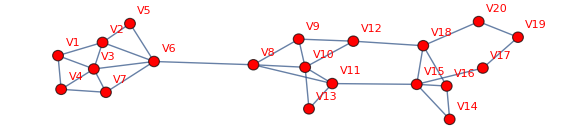

```mathematica
(**************************************************** Task 1.1 ***********************)
edges={
V1<->V2,V1<->V3,V1<->V4,V2<->V3,V2<->V5,V2<->V6,V3<->V4,V3<->V6,V3<->V7,V4<->V7,V5<->V6,V6<->V7,
V8<->V9,V8<->V10,V8<->V11,V9<->V10,V9<->V12,V10<->V11,V10<->V12,V10<->V13,V11<->V13,
V14<->V15,V14<->V16,V15<->V16,V15<->V17,V15<->V18,V16<->V18,V17<->V19,V18<->V20,V19<->V20,

V6<->V8,V11<->V15,V12<->V18 };

 
g=Graph[edges,VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,EdgeStyle->{Thick}
, VertexSize->Large, VertexStyle->Red]
```

```mathematica
(**************************************************** Task 1.2 ***********************)
```

```mathematica
adjacencyMatrix = AdjacencyMatrix[g];
degreeMatrix=DiagonalMatrix[Total[adjacencyMatrix,{2}]];
laplacianMatrix=degreeMatrix-adjacencyMatrix;
MatrixForm[laplacianMatrix]
```

(3 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 4 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 5 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 3 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | -1 | 5 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | -1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 4 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 3 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 5 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 4 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 5 | -1 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 3 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 4 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 2)

```mathematica
(**************************************************** Task 1.3 ***********************)
{eigenvalues,eigenvectors}=N[Eigensystem[laplacianMatrix]];
eigenvalues;
eigenvectors;
```

```mathematica
(**************************************************** Task 1.4 ***********************)
k = 20;
```

```mathematica
(**************************************************** Task 1.5 ***********************)
eigenpairs=Transpose[{eigenvalues,eigenvectors}];

sortedEigenpairs=SortBy[eigenpairs,First];

smallestFourVectors=Transpose[sortedEigenpairs[[;;k,2]]];

V = MatrixForm[smallestFourVectors]
```

(1. | -1.28317 | 0.385664 | -0.095979 | -13.4904 | 0.0475203 | 0.0352105 | -6.03826 | 12.9991 | 0.618907 | -0.0367576 | -4.19037 | -0.00183788 | 396.093 | 7.45445 | -0.573419 | 0.176437 | 0.999808 | 1.05862 | -2.58774
1. | -1.19313 | 0.267826 | -0.03695 | 12.6193 | -0.0614382 | 0.0650752 | -2.52572 | 5.2572 | 0.423862 | -0.118314 | -59.8506 | 0.307845 | -185.626 | -8.19695 | 0.882183 | -8.23371 | 3.96983 | 0.294061 | -2.64655
1. | -1.2185 | 0.307106 | -0.0621236 | -8.62368 | 0.0332395 | -0.00414152 | 0.0055998 | 0.176006 | 0.132557 | -0.0620285 | -31.7926 | 0.158977 | -127.814 | -3.21997 | 0.235249 | 9.40996 | -8.82183 | -4.94023 | 8.93946
1. | -1.2871 | 0.393665 | -0.103181 | -24.4995 | 0.0986849 | -0.0197231 | -0.0864666 | -1.59293 | -0.602366 | 0.198032 | 94.5756 | -0.46866 | -400.408 | -3.48462 | 0.0294061 | -2.47011 | 0.940996 | -1.17624 | -4.46973
1. | -1.15309 | 0.205266 | 0.0030081 | 43.7747 | -0.198729 | 0.149739 | -0.251847 | -3.75123 | -0.881035 | 0.17322 | 59.6319 | -0.18195 | 169.247 | 2.20546 | -0.205843 | -0.588122 | -2.94061 | -4.23448 | 2.35249
1. | -0.977567 | 0.0424338 | 0.0402807 | 10.1387 | -0.0345994 | -0.0395424 | 2.66868 | -2.61395 | 0.521705 | -0.139456 | -41.5693 | 0.0301528 | -288.672 | 1.30662 | -0.562851 | 6.5934 | 2.57304 | 7.55829 | -22.8357
1. | -1.20838 | 0.295921 | -0.0593296 | -15.1225 | 0.0656143 | -0.0541583 | 5.99532 | -13.6456 | -0.707125 | 0.00321629 | -30.28 | 0.284872 | 453.303 | 2.70536 | 0.117624 | -4.99904 | 1.41149 | -0.352873 | 4.46973
1. | 0.000143157 | -0.884678 | 0.320839 | 3.03906 | 0.0407939 | -0.281871 | 3.26623 | 5.96374 | 2.03606 | -0.207551 | 8.2709 | -0.545765 | -366.272 | 6.34414 | -1.02921 | -2.57304 | 2.76601 | -1.02921 | 10.4208
1. | 0.278574 | -1.12758 | 0.445569 | 1.37111 | 0.682711 | -0.749003 | 1.08357 | 8.1038 | -0.178153 | 0.180414 | 18.4856 | 4.39728 | 282.801 | -5.65264 | -0.562851 | 2.05843 | 1.35084 | -2.44438 | -2.57304
1. | 0.312782 | -1.1239 | 0.38596 | -1.41403 | 0.00310885 | -0.0799571 | 0.19169 | 2.22575 | -0.0149939 | 0.0129406 | 4.86892 | -0.659309 | -15.5385 | 2.11898 | 1.11515 | -5.88883 | -11.6048 | 7.49396 | -4.31385
1. | 0.386766 | -0.897502 | 0.125129 | -2.43765 | -0.549919 | 0.256665 | 0.732272 | 0.00954837 | 1.55664 | -0.160815 | 20.6898 | -3.78719 | 315.181 | -4.11686 | 1.01313 | 1.67247 | 1.67247 | -7.4618 | -6.43259
1. | 0.490066 | -0.823353 | 0.23214 | 0.458899 | 0.968737 | -0.514975 | -2.99035 | -5.79545 | -2.00761 | 0.106665 | -26.0912 | -3.01377 | -127.884 | 2.77405 | 1.04932 | 3.13589 | 5.06566 | 0.578933 | 4.05253
1. | 0.371606 | -1.33734 | 0.461571 | -7.40865 | -1.1315 | 1.03567 | -1.62567 | -3.17264 | -1.43609 | 0.101514 | -15.0286 | 2.27251 | -106.922 | 0.651299 | -0.675422 | 1.19003 | 2.50871 | 0.771911 | 2.18708
1. | 0.902245 | 0.309729 | -2.07346 | 0.782515 | -0.21444 | 0.0340436 | 2.96185 | 15.3326 | -1.23262 | 0.833975 | -13.8602 | -1.01213 | -55.8107 | 0.651299 | -0.273385 | -0.804073 | -0.578933 | -1.28652 | -2.57304
1. | 0.81709 | 0.194338 | -0.77956 | -0.35898 | -0.277999 | -0.116723 | -0.783972 | -5.00409 | 0.857092 | 0.00904583 | 8.08697 | -1.21365 | 235.939 | -5.10185 | -0.675422 | 3.13589 | 2.12275 | 14.4733 | 10.2278
1. | 0.881386 | 0.273817 | -1.51634 | 0.765801 | 0.174368 | 0.122536 | -0.899264 | -5.7992 | 0.466555 | -1.24262 | 15.4869 | 3.19591 | -79.4898 | 3.27308 | 1.73454 | 0.54878 | 0.849303 | -1.48955 | -0.365853
1. | 0.997785 | 1.00709 | 0.605146 | -1.11464 | -1.12942 | -1.00947 | -2.13538 | -8.98799 | 0.519311 | 0.82873 | -6.73788 | 1.18884 | -96.3406 | 2.05039 | 0.326655 | -0.743768 | -0.44224 | -2.89466 | -2.33181
1. | 0.82126 | 0.183626 | -0.342345 | 0.740398 | 0.751071 | 0.226127 | -2.56598 | -12.0416 | 0.341154 | -0.24507 | -5.07452 | -0.843586 | -36.822 | -1.94938 | -2.71174 | -3.86357 | -4.01635 | -4.95711 | -4.93701
1. | 1.06124 | 1.32788 | 1.44963 | -0.220509 | -0.267809 | -0.0555076 | 1.99764 | 11.337 | -1.41495 | -1.23535 | 3.3739 | -1.11659 | 34.0198 | -1.03173 | -0.425154 | -0.0522648 | -0.116591 | 0.458322 | 0.2171
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
(**************************************************** Task 1.6 ***********************)
clusters=FindClusters[smallestFourVectors,k]
```

{{{1.,-1.28317,0.385664,-0.095979,-13.4904,0.0475203,0.0352105,-6.03826,12.9991,0.618907,-0.0367576,-4.19037,-0.00183788,396.093,7.45445,-0.573419,0.176437,0.999808,1.05862,-2.58774}},{{1.,-1.19313,0.267826,-0.03695,12.6193,-0.0614382,0.0650752,-2.52572,5.2572,0.423862,-0.118314,-59.8506,0.307845,-185.626,-8.19695,0.882183,-8.23371,3.96983,0.294061,-2.64655}},{{1.,-1.2185,0.307106,-0.0621236,-8.62368,0.0332395,-0.00414152,0.0055998,0.176006,0.132557,-0.0620285,-31.7926,0.158977,-127.814,-3.21997,0.235249,9.40996,-8.82183,-4.94023,8.93946}},{{1.,-1.2871,0.393665,-0.103181,-24.4995,0.0986849,-0.0197231,-0.0864666,-1.59293,-0.602366,0.198032,94.5756,-0.46866,-400.408,-3.48462,0.0294061,-2.47011,0.940996,-1.17624,-4.46973}},{{1.,-1.15309,0.205266,0.0030081,43.7747,-0.198729,0.149739,-0.251847,-3.75123,-0.881035,0.17322,59.6319,-0.18195,169.247,2.20546,-0.205843,-0.588122,-2.94061,-4.23448,2.35249}},{{1.,-0.977567,0.0424338,0.0402807,10.1387,-0.0345994,-0.0395424,2.66868,-2.61395,0.521705,-0.139456,-41.5693,0.0301528,-288.672,1.30662,-0.562851,6.5934,2.57304,7.55829,-22.8357}},{{1.,-1.20838,0.295921,-0.0593296,-15.1225,0.0656143,-0.0541583,5.99532,-13.6456,-0.707125,0.00321629,-30.28,0.284872,453.303,2.70536,0.117624,-4.99904,1.41149,-0.352873,4.46973}},{{1.,0.000143157,-0.884678,0.320839,3.03906,0.0407939,-0.281871,3.26623,5.96374,2.03606,-0.207551,8.2709,-0.545765,-366.272,6.34414,-1.02921,-2.57304,2.76601,-1.02921,10.4208}},{{1.,0.278574,-1.12758,0.445569,1.37111,0.682711,-0.749003,1.08357,8.1038,-0.178153,0.180414,18.4856,4.39728,282.801,-5.65264,-0.562851,2.05843,1.35084,-2.44438,-2.57304}},{{1.,0.312782,-1.1239,0.38596,-1.41403,0.00310885,-0.0799571,0.19169,2.22575,-0.0149939,0.0129406,4.86892,-0.659309,-15.5385,2.11898,1.11515,-5.88883,-11.6048,7.49396,-4.31385}},{{1.,0.386766,-0.897502,0.125129,-2.43765,-0.549919,0.256665,0.732272,0.00954837,1.55664,-0.160815,20.6898,-3.78719,315.181,-4.11686,1.01313,1.67247,1.67247,-7.4618,-6.43259}},{{1.,0.490066,-0.823353,0.23214,0.458899,0.968737,-0.514975,-2.99035,-5.79545,-2.00761,0.106665,-26.0912,-3.01377,-127.884,2.77405,1.04932,3.13589,5.06566,0.578933,4.05253}},{{1.,0.371606,-1.33734,0.461571,-7.40865,-1.1315,1.03567,-1.62567,-3.17264,-1.43609,0.101514,-15.0286,2.27251,-106.922,0.651299,-0.675422,1.19003,2.50871,0.771911,2.18708}},{{1.,0.902245,0.309729,-2.07346,0.782515,-0.21444,0.0340436,2.96185,15.3326,-1.23262,0.833975,-13.8602,-1.01213,-55.8107,0.651299,-0.273385,-0.804073,-0.578933,-1.28652,-2.57304}},{{1.,0.81709,0.194338,-0.77956,-0.35898,-0.277999,-0.116723,-0.783972,-5.00409,0.857092,0.00904583,8.08697,-1.21365,235.939,-5.10185,-0.675422,3.13589,2.12275,14.4733,10.2278}},{{1.,0.881386,0.273817,-1.51634,0.765801,0.174368,0.122536,-0.899264,-5.7992,0.466555,-1.24262,15.4869,3.19591,-79.4898,3.27308,1.73454,0.54878,0.849303,-1.48955,-0.365853}},{{1.,0.997785,1.00709,0.605146,-1.11464,-1.12942,-1.00947,-2.13538,-8.98799,0.519311,0.82873,-6.73788,1.18884,-96.3406,2.05039,0.326655,-0.743768,-0.44224,-2.89466,-2.33181}},{{1.,0.82126,0.183626,-0.342345,0.740398,0.751071,0.226127,-2.56598,-12.0416,0.341154,-0.24507,-5.07452,-0.843586,-36.822,-1.94938,-2.71174,-3.86357,-4.01635,-4.95711,-4.93701}},{{1.,1.06124,1.32788,1.44963,-0.220509,-0.267809,-0.0555076,1.99764,11.337,-1.41495,-1.23535,3.3739,-1.11659,34.0198,-1.03173,-0.425154,-0.0522648,-0.116591,0.458322,0.2171}},{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
(**************************************************** Task 1.7 ***********************)
vertices=VertexList[g];

clusters=FindClusters[vertices,k];

clusterLabels=Table[With[{clusterIndex=Position[clusters,SelectFirst[clusters,MemberQ[#,vertices[[i]]]&]]},If[clusterIndex==={},Missing[],First[First[clusterIndex]]]],{i,Length[vertices]}]

vertexColors=Table[ColorData["Rainbow"][clusterLabels[[i]]/Max[clusterLabels]],{i,Length[vertices]}];
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

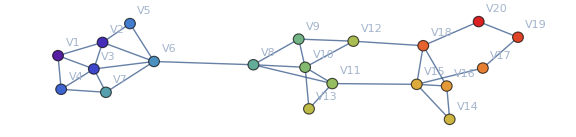

```mathematica
(**************************************************** Task 1.8 ***********************)
coloredGraph=
Graph[
vertices,
EdgeList[g],
VertexStyle->Thread[vertices->vertexColors],
VertexLabels->"Name",
VertexSize->Large,
EdgeStyle->Thick, 
ImageSize->Large
]
```

```mathematica
(**************************************************** Task 1.8 ***********************)
```

Clusters: {{V1,V10,V11,V13,V14,V15,V16,V19},{V2,V3,V4,V5,V6,V7,V8,V9,V12,V17,V18,V20}}